## Math 137 Sp 19 Mathematica Hw 2 Surfaces of revolution. Ernst

Form groups of two. Each member of the group must understand and be able to explain (in detail) all of the homework turned in. We allow you to work in groups so that you have someone with whom you can talk about your work in detail. This is not meant for group members to only do half of the work. 
Each group turns in one (stapled) printout at the beginning of class. In addition you need to submit this electronically via a Blackboard link.

Due: Friday, February 22.

### Plot a surface using ParametricPlot3D

#### Example 1 f(x)=x/5 Cos[x] over the interval [1,3]. Rotate around the x-axis

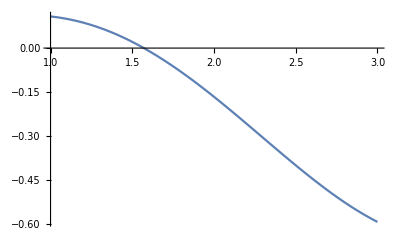

```mathematica
f[x_]:=x/5 Cos[x]
Plot[f[x],{x,1,3}]
```

How do we rotate?
For each point on the function of the form (x,f(x)) we now get a circle of points.
The circle has radius |f(x)| and center (x,0,0) and is perpendicular to the x-axis.

We can use trigonometry to plot such a circle as

(x,f(x) sin(t),f(x)cos(t))

where the parameter t goes from 0 to 2π

For example let x=2

```mathematica
?ParametricPlot3D
```

RowBox[{"ParametricPlot3D", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["z", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] produces a three-dimensional space curve parametrized by a variable StyleBox["u", "TI"] which runs from SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"ParametricPlot3D", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["z", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] produces a three-dimensional surface parametrized by StyleBox["u", "TI"] and StyleBox["v", "TI"]. 
RowBox[{"ParametricPlot3D", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["z", "TI"]]}], "}"}], ",", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["g", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["g", "TI"], StyleBox["y", "TI"]], ",", SubscriptBox[StyleBox["g", "TI"], StyleBox["z", "TI"]]}], "}"}], StyleBox["…", "TR"]}]}], "}"}], StyleBox["…", "TR"]}], "]"}] plots several objects together. 
RowBox[{"ParametricPlot3D", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"]}], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes parameters RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"]}], "}"}] to be in the geometric region StyleBox["reg", "TI"].

```mathematica
g[t_]:={2,f[2]Sin[t],f[2]Cos[t]}
ParametricPlot3D[g[t],{t,0,2π},AxesLabel->{"x","y","z"},PlotStyle->Thickness[.01]]
```

-Graphics3D-

Now we put all such circles together, that is we let x vary from 1 to 3.

```mathematica
myplotone=ParametricPlot3D[{x,f[x]Sin[t],f[x]Cos[t]},{x,1,3},{t,0,2π},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

Here we create a movie as the t-interval increases from a very small interval [0,0.01] to the full interval [0,2π].

```mathematica
Manipulate[ParametricPlot3D[{x,f[x]Sin[t],f[x]Cos[t]},{x,1,3},{t,0.01,a},PlotRange->{{1,3},{-1,1},{-1,1}}],{a,0,2π}]
```

#### Example 1I f(x)=x Cos[3t] over the interval [1,3]. Rotate around the axis y=2

```mathematica
f[x_]:=x Cos[x]
Plot[f[x],{x,1,3}]
```

How do we rotate?
For each point on the function of the form (x,f(x)) we now get a circle of points.
The circle has radius |f(x)-2| and center (x,5,0) and is perpendicular to the x-axis.

We can use trigonometry to plot such a circle as

(x,|f(x)-2| sin(t),|f(x)-2| cos(t))

where the parameter t goes from 0 to 2π

For example let x=2

```mathematica
g[t_]:={2,Abs[f[2]-2]Sin[t],Abs[f[2]-2]Cos[t]}+{0,5,0}
ParametricPlot3D[g[t],{t,0,2π},AxesLabel->{"x","y","z"},PlotStyle->Thickness[.01]]
```

Now we put all such circles together, that is we let x varie from 1 to 3

```mathematica
myplottwo=ParametricPlot3D[{x,Abs[f[x]-2]Sin[t],Abs[f[x]-2]Cos[t]}+{0,2,0},{x,1,3},{t,0,2π},AxesLabel->{"x","y","z"}]
```

Let us put some axis into the plot: The blue are the x,y,z axis and the red is the axis of rotation.

```mathematica
coordinateaxis=Show[{Graphics3D[{Blue,Thickness[.05],Line[{{0,0,0},{0,0,5}}],Line[{{0,0,0},{0,5,0}}],Line[{{0,0,0},{5,0,0}}]}],
Graphics3D[{Red,Thickness[.05],Line[{{0,2,0},{5,2,0}}]}]}]
```

```mathematica
Show[myplottwo,coordinateaxis,PlotRange->{{0,3},{-4,7},{-5,5}}]
```

#### Example 1II f(x)=x/5 Cos[3t] over the interval [1,3]. Rotate around the Y-axis

```mathematica
f[x_]:=x/5 Cos[x]
Plot[f[x],{x,1,3}]
```

How do we rotate?
For each point on the function of the form (x,f(x)) we now get a circle of points.
The circle has radius |x| and center (0,0,f(x)) and is perpendicular to the x-axis.

We can use trigonometry to plot such a circle as

(x cos(t),x sin(t),f(x))

where the parameter t goes from 0 to 2π

For example let x=2

```mathematica
g[t_]:={2 Cos[t],2Sin[t],f[2]}
ParametricPlot3D[g[t],{t,0,2π},AxesLabel->{"x","y","z"},PlotStyle->Thickness[.01]]
```

-Graphics3D-

```mathematica
myplotthree=ParametricPlot3D[{x Cos[t],x Sin[t],f[x]},{x,-8,2.5},{t,0,2π},AxesLabel->{"x","z","y"}]
```

-Graphics3D-

Here is the movie as before

```mathematica
Manipulate[ParametricPlot3D[{x Cos[t],x Sin[t],f[x]},{x,1,3},{t,0.01,a},PlotRange->{{-3,3},{-3,3},{-1,1}},AspectRatio->1],{a,0,2π}]
```

```mathematica
Show[myplotone,myplotthree,PlotRange->All]
```

### Can we do calculus? Compute the volume of revolutions for all three volumes!

Compute the volume of revolutions for both volumes!

#### Example 1 f(x)=x/5 Cos[x] over the interval [1,3]. Rotate around the x-axis

Rotation about x-axis

```mathematica
f[x_]:=x/5 Cos[x]
```

```mathematica
∫_1^3 π f[x]^2 ⅆx
N[%]
```

#### Example 1I f(x)=x Cos[3t] over the interval [1,3]. Rotate around the axis y=2

Rotation about axis y=2

```mathematica
f[x_]:=x Cos[x]
```

```mathematica
∫_1^3 π (f[x]-2)^2 ⅆx
N[%]
```

#### Example 1II f(x)=x/5 Cos[3t] over the interval [1,3]. Rotate around the x-axis y=0

Rotation about y-axis

```mathematica
f[x_]:=x/5 Cos[x]
```

```mathematica
∫_1^3 2π x Abs[f[x]]ⅆx
N[%]
```

### Your Homework:

#### Problem 1 What kind of shape is this?

Let a>b>0 and c>0 be three positive parameters. Consider the parametric equations:
{(a+b cos(s))cos(t), (a+b cos(s))sin(t),c sin(s)},
where 0≤t≤2π and 0≤s≤2π.
(i) Use a ParametricPlot3D to graph these surfaces for at least 5 different choices of a,b and c. What kind of shape do you get?
(ii) Describe the role of each of the parameters a,b and c.
(iii) Compute the surface area and volume of the surface you generated for 
(a) a=6, b=1,c=1
(b) a=6, b=2,c=2
(c) a=6, b=4,c=3

#### Problem II Design a champagne glass with a volume of about 225 ml.

Warning: This will not be easy - so start early.

```mathematica
f[x_]:=√((-k^2 x^2+4096(1+x^2/64))/(4096(1+x^2/64)))
```

```mathematica
2π*Integrate[f[x], {x, -8, 2.5}]
```

279.014

```mathematica
?NSolve
```

NSolve[expr,vars] attempts to find numerical approximations to the solutions of the system expr of equations or inequalities for the variables vars. 
NSolve[expr,vars,Reals] finds solutions over the domain of real numbers.

```mathematica
Integrate[√((x^2+4096(1+x^2/64))/(4096(1+x^2/64))), {x, -8, 2.5}]
```

10.514+3.33067×10^-16 ⅈ

```mathematica
2π*Integrate[√((1.5110751167862926*^-14-82.96061902437413 ⅈ*x^2+4096(1+x^2/64))/(4096(1+x^2/64))), {x, -8, 2.5}]
```

2 π ∫_-8^2.5 1/64 √((1.51108×10^-14-(0.+82.9606 ⅈ) x^2+4096 (1+x^2/64))/(1+x^2/64))ⅆx

```mathematica
FindInstance[{35.81== Integrate[√((-k^2 x^2+4096(1+x^2/64))/(4096(1+x^2/64))), {x, -8, 2.5}]}, k]
```

{{k→1.51108×10^-14-82.9606 ⅈ}}

```mathematica
Integrate[√((-k^2 x^2+4096(1+x^2/64))/(4096(1+x^2/64))), {x, -8, 2.5}]
```

-6.25437×10^-17 √(519.884-0.722703 k^2)-(0.+8. ⅈ) EllipticE[ⅈ ArcSinh[1],1-k^2/64]

```mathematica
TrigToExp[-6.254370395523848*^-17 √(519.8835291641212-0.7227028597143597 k^2)-(0.+8. ⅈ) EllipticE[ⅈ ArcSinh[1],1-k^2/64]]
```

-6.25437×10^-17 √(519.884-0.722703 k^2)-(0.+8. ⅈ) EllipticE[ⅈ Log[1+√2],1-k^2/64]

```mathematica
NSolve[225==π*k^2*Integrate[1-y^2/64, {y, -8, 0}], k]
```

{{k→-3.66452},{k→3.66452}}

```mathematica
π*Integrate[(3.0395602316299635 √(1-y^2/64))^2, {y, -8, 2.5}]
```

225.

```mathematica
π*Integrate[(3.6645188392718997 √(1-y^2/64))^2, {y, -8, 0}]
```

225.

```mathematica
f[t_]:=3.0395602316299635 √(1-t^2/64)
```

```mathematica
new[x_]:=√(9.2355-.144 x^2)
```

```mathematica
π*Integrate[(new[x])^2, {x, -8, 2.5}]
```

225.085

```mathematica
z[x_]:=√(64-4.766 x^2)
```

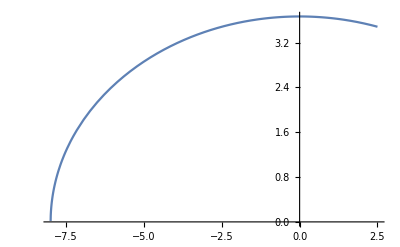

```mathematica
Plot[new[t], {t, -8, 2.5}]
```

```mathematica
f[x]
```

3.03956 √(1-x^2/64)

```mathematica
g[t_]:={2 Cos[t],2Sin[t],f[2]}
ParametricPlot3D[g[t],{t,0,2π},AxesLabel->{"x","y","z"},PlotStyle->Thickness[.01]]
```

```mathematica
ParametricPlot3D[g[x], x Cos[t], x Sin[t], {x, -8, 2.5}, {t, 0, 2π}, AxesLabel->{"x", "z", "y"}]
```

ParametricPlot3D::nonopt: Options expected (instead of {t,0,2 π}) beyond position 3 in ParametricPlot3D[g[x],x Cos[t],x Sin[t],{x,-8,2.5},{t,0,2 π},AxesLabel→{x,z,y}]. An option must be a rule or a list of rules.

ParametricPlot3D[g[x],x Cos[t],x Sin[t],{x,-8,2.5},{t,0,2 π},AxesLabel→{x,z,y}]

```mathematica
cylinder[x_]:= Sin[2x]
```

```mathematica
graphcylinder=ParametricPlot3D[{x, cylinder[x]Sin[t], cylinder[x]Cos[t]}, {x, -5π, -8}, {t, 0, 2π}, AxesLabel->{"x","z","y"}, Mesh->None, ColorFunction->ColorData["SunsetColors"]]
```

-Graphics3D-

```mathematica
cup=ParametricPlot3D[{x ,new[x] Sin[t],new[x]Cos[t]},{x,-8, 2.5},{t,0,2π},AxesLabel->{"x","z","y"},Mesh->None, ColorFunction->(Directive[Opacity[#3],ColorData["ThermometerColors"][#1]]&)]
```

-Graphics3D-

```mathematica
bottom[x_]:=3Sin[3x]
bottomgraph=ParametricPlot3D[{x ,bottom[x] Sin[t],bottom[x]Cos[t]},{x,-5.2π, -5π},{t,0,2π},AxesLabel->{"x","z","y"}, Mesh->None, ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Show[cup, graphcylinder,bottomgraph,PlotRange-> {{-20,5},{-5, 5},{-5, 5}}]
```

-Graphics3D-

```mathematica
?ParametricPlot3D
```

ParametricPlot3D[{f_x,f_y,f_z},{u,u_min,u_max}] produces a three-dimensional space curve parametrized by a variable u which runs from u_min to u_max. 
ParametricPlot3D[{f_x,f_y,f_z},{u,u_min,u_max},{v,v_min,v_max}] produces a three-dimensional surface parametrized by u and v. 
ParametricPlot3D[{{f_x,f_y,f_z},{g_x,g_y,g_z},…},…] plots several objects together. 
ParametricPlot3D[…,{u,v}∈reg] takes parameters {u,v} to be in the geometric region reg.

The class needs to have a stem and a base - see the above. 
- use ParametricPlot3D[] to construct the pieces and put them together with Show[]. You turned in work must contain the functions which you used.
- do an integral calculation to compute the volume. The volume the volume should be any value between 224 and 226 ml. The integral should be done in Mathematica. If you integral is complicated you it will be enough to only evaluate it numerically using NIntegrate[].
- The shape of the class part that will contain the champagne cannot be a cone or cylinder - that is to simple! (After all you don’t need an integral to compute the volume of a cone or cylinder. )
- Make your glass look pretty by looking for shape, color and proportions.

#### Past solutions

-Graphics-